```mathematica
<<EDCRGTCcode`
```

SetDelayed::write: Tag Classify in Classify[x_] is Protected.

```mathematica
Coord={t,x};
g={{v[t,x]^2-1,-v[t,x]},{-v[t,x],1}};
(*g={{-f[t,x],0},{0,1/f[t,x]}};*)
RGtensors[g,Coord,{1,1,1}]
```

gdd = (-1+v[t,x]^2 | -v[t,x]
-v[t,x] | 1)

LineElement = d[x]^2-2 d[t] d[x] v[t,x]+d[t]^2 (-1+v[t,x]) (1+v[t,x])

gUU = (-1 | -v[t,x]
-v[t,x] | -(-1+v[t,x]) (1+v[t,x]))

gUU computed in 0. sec

Gamma computed in 0. sec

Riemann(dddd) computed in 0.016 sec

Riemann(Uddd) computed in 0. sec

Ricci computed in 0. sec

Weyl computed in 0. sec

Conformally Flat

Einstein computed in 0. sec

Einstein Space

All tasks completed in 0.015625 seconds

```mathematica
{R,Rdd//MatrixForm,EUd//MatrixForm,multiDot[Rdddd,Raise[Rdddd,1,2,3,4],{1,1},{2,2},{3,3},{4,4}]//Simplify,Transpose[GUdd,{3,1,2}]//MatrixForm}
```

{2 ((v^(0,1)[t,x])^2+v[t,x] v^(0,2)[t,x]+v^(1,1)[t,x]),((-1+v[t,x]) (1+v[t,x]) ((v^(0,1)[t,x])^2+v[t,x] v^(0,2)[t,x]+v^(1,1)[t,x]) | -v[t,x] ((v^(0,1)[t,x])^2+v[t,x] v^(0,2)[t,x]+v^(1,1)[t,x])
-v[t,x] ((v^(0,1)[t,x])^2+v[t,x] v^(0,2)[t,x]+v^(1,1)[t,x]) | (v^(0,1)[t,x])^2+v[t,x] v^(0,2)[t,x]+v^(1,1)[t,x]),(0 | 0
0 | 0),4 ((v^(0,1)[t,x])^2+v[t,x] v^(0,2)[t,x]+v^(1,1)[t,x])^2,((v[t,x]^2 v^(0,1)[t,x]
-v[t,x] v^(0,1)[t,x]+v[t,x]^3 v^(0,1)[t,x]-v^(1,0)[t,x]) | (-v[t,x] v^(0,1)[t,x]
-v[t,x]^2 v^(0,1)[t,x])
(-v[t,x] v^(0,1)[t,x]
-v[t,x]^2 v^(0,1)[t,x]) | (v^(0,1)[t,x]
v[t,x] v^(0,1)[t,x]))}

```mathematica
A={A0[t,x],A1[t,x]};
(*various ways to write LHS of Proca equation, the difference is zero, using Lorenz condition*)
covDiv[Raise[covD[A,{1}],2]-Transpose[Raise[covD[A,{1}],2]],{1,{2}}]-(Laplacian[A,{1}]-Raise[Rdd,1].A)//FullSimplify
covDiv[Raise[covD[A,{1}],2],{1,{2}}]-covDiv[Raise[covD[A,{1}],2],{{1},2}]-(Laplacian[A,{1}]-gUU.multiDot[Rdd,A,{1,1}])//FullSimplify
```

{v[t,x] (A1^(0,2)[t,x]+A0^(1,1)[t,x])+A1^(1,1)[t,x]+A0^(2,0)[t,x],(-1+v[t,x]^2) A1^(0,2)[t,x]+(-1+v[t,x]^2) A0^(1,1)[t,x]+v[t,x] (A1^(1,1)[t,x]+A0^(2,0)[t,x])}

{v[t,x] (A1^(0,2)[t,x]+A0^(1,1)[t,x])+A1^(1,1)[t,x]+A0^(2,0)[t,x],(-1+v[t,x]^2) A1^(0,2)[t,x]+(-1+v[t,x]^2) A0^(1,1)[t,x]+v[t,x] (A1^(1,1)[t,x]+A0^(2,0)[t,x])}

```mathematica
(*Proca equation*)
Collect[Laplacian[A,{1}]-gUU.Rdd.A-m^2 A/.{Derivative[1,1][A1][t,x]-> -Derivative[2,0][A0][t,x],Derivative[1,1][A0][t,x]-> -Derivative[0,2][A1][t,x]}//FullSimplify,{Derivative[0,2][A0][t,x],Derivative[0,1][A0][t,x],Derivative[1,0][A0][t,x],Derivative[2,0][A0][t,x],A0[x,t],Derivative[0,2][A1][t,x],Derivative[0,1][A1][t,x],Derivative[1,0][A1][t,x],Derivative[2,0][A1][t,x],A1[x,t]}]
```

{2 A1^(0,1)[t,x] v^(0,1)[t,x]+(1-v[t,x]^2) A0^(0,2)[t,x]+2 v[t,x] A1^(0,2)[t,x]+A1[t,x] v^(0,2)[t,x]-v^(0,1)[t,x] A0^(1,0)[t,x]+A0^(0,1)[t,x] (-4 v[t,x] v^(0,1)[t,x]-v^(1,0)[t,x])-A0[t,x] (m^2+2 (v^(0,1)[t,x])^2+2 v[t,x] v^(0,2)[t,x]+v^(1,1)[t,x])-A0^(2,0)[t,x],(1-v[t,x]^2) A1^(0,2)[t,x]-v^(0,1)[t,x] A1^(1,0)[t,x]+2 v[t,x] A0^(0,1)[t,x] v^(1,0)[t,x]-A1^(0,1)[t,x] v^(1,0)[t,x]+2 A0[t,x] v^(0,1)[t,x] v^(1,0)[t,x]+A0^(1,0)[t,x] (2 v[t,x] v^(0,1)[t,x]+2 v^(1,0)[t,x])+2 A0[t,x] v[t,x] v^(1,1)[t,x]-A1[t,x] (m^2+v^(1,1)[t,x])+2 v[t,x] A0^(2,0)[t,x]-A1^(2,0)[t,x]+A0[t,x] v^(2,0)[t,x]}

```mathematica
covDiv[A,{1}]
```

A1^(0,1)[t,x]+A0^(1,0)[t,x]

```mathematica
(*field tensor*)
F={{0,-e[t,x]},{e[t,x],0}};
covDiv[F,{{1},2}]//MatrixForm
```

(e^(0,1)[t,x]
-e^(1,0)[t,x])

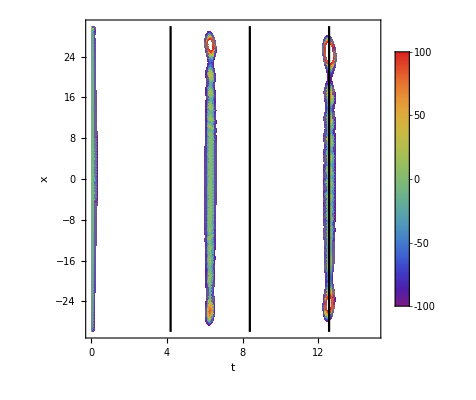

```mathematica
a=60;(*box length*)
tm=15;(*time length*)
omega=3;
beta=30;
mu=100;
u0[x_]:=(omega/Pi)^(1/4)Exp[-x^2/2];(*initial wave function*)
sol=NDSolve[{-Laplacian[u[t,x],{x}]/2+u[t,x]+0.5*omega^2(x-beta*Sin[mu*t])^2==I*D[u[t,x],t],u[t,-a/2]==u[t,a/2],u[0,x]==u0[x]},u,{t,0,tm},{x,-a/2,a/2}];
Show[DensityPlot[Re[u[t,x]/.sol],{t,0,tm},{x,-a/2,a/2},FrameLabel->{t,x},PlotLegends->Automatic,PlotPoints->100,ColorFunction->"Rainbow",PlotRange-> {-100,100}],
ParametricPlot[{{2Pi/(omega/2),y},{{2*2Pi/(omega/2),y}},{{3*2Pi/(omega/2),y}}},{y,-a/2,a/2},PlotStyle->Black]
]
```